```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]];
If[!MemberQ[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]],AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]]];
Print["Package path ",FindFile["GDCAnalysis3`"]];
Print["Package path ",FindFile["GDCComparisons`"]];
Print["Package path ",FindFile["GDCAnalysis5`"]];
<<GDCAnalysis3`
<<GDCComparisons`
<<GDCAnalysis5`
```

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis3.m

Package path /home/carla/GDC/DialecticalStructures/GDCComparisons.m

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis5.m

```mathematica
(*nEFUN[persInds[[#]],,numCONE]*)
nEFUN[name_, pos_, mod_]:=Module[{ind,pers,posP,con,conE,persE,persEB,persEA,persET,out},
(*{3,7,9,11,15,19}*)
Which[name=="DLB", ind=3; posP=pos;,
name=="MUR", ind=7;posP=Drop[pos,1];,
name=="LYE", ind=9;posP=Drop[pos,1];,
name=="PHI", ind=11;posP=Drop[pos,2];,
name=="SED", ind=15;posP=Drop[pos,3];,
name=="AUS", ind=19;posP=Drop[pos,6];];

pers=posP[[All,ind]];
con=posP[[All,1]];
persE=Map[Union[#["BK"],#["EV"]]&,pers];
conE=Map[Union[#["BK"],#["EV"]]&,con];


persEB=Map[Union[persE[[#]],conE[[#]]]&,Range[Length[conE]]];
persEA=Map[Union[persE[[#]],conE[[#+1]]]&,Range[Length[conE]-1]];
persET=Flatten[Prepend[Map[{persEA[[#]],persEB[[#+1]]}&,Range[Length[conE]-1]],{First[persEB]}],1];
(*Print["persET ", persET];*)

out=If[mod=="NUM",Map[Length[#]&,persET],persET];
Return[out];
];

eFUN[name_, pos_,dev_, mod_]:=Module[{persE,persENEG, false,true, out},
persE=nEFUN[name, pos, "STR"];
persENEG=Map[Function[y,Map[Function[x,If[StringQ[x],!x,x[[1]]]],y]],persE];
(*Print["persENEG ", persENEG];*)
false=Map[Intersection[dev,#]&,persENEG];
true=Map[Intersection[dev,#]&,persE];
out=Which[mod=="FALN", Map[Length[#]&,false],
mod=="FAL",false,
mod=="TRUN", Map[Length[#]&,true],
mod=="TRU",true];
Return[out];
];

prozEFunc[name_, eL_,sens_]:=Module[{sentPers,sentPT,out},
sentPers=Which[name=="DLB",Drop[sens,0],
name=="MUR", Drop[sens,1],
name=="LYE", Drop[sens,1],
name=="PHI", Drop[sens,2],
name=="SED",Drop[sens,3],
name=="AUS",Drop[sens,6]];
sentPT=Flatten[Prepend[Map[{sentPers[[#+1]],sentPers[[#+1]]}&,Range[Length[sentPers]-1]],{sentPers[[1]]}],1];
(*Print["sentPT ", sentPT];*)
out=Map[Round[ eL[[#]]/(sentPT[[#]]-15.),0.001]&,Range[Length[sentPT]]];
Return[out];
];

h[nam_,lTS_]:=Module[{list,k},
k=If[lTS>9,2,1];
list=Which[nam=="DLB",Drop[Range[lTS],0*k],
nam=="MUR",Drop[Range[lTS],1*k],
nam=="LYE",Drop[Range[lTS],1*k],
nam=="PHI",Drop[Range[lTS],2*k],
nam=="SED",Drop[Range[lTS],3*k],
nam=="AUS",Drop[Range[lTS],6*k]
];
Return[list];];

singlePlot2[nam_, dataArrows_,poi_,colS_,conf_, range_, fac1_,fac2_]:=Module[{head,arrows,size, plot1,pointsG,plot2,dataInset,boxInset},

head=Graphics[{Thickness[0.007],Line[{{{-1,1/2},{0,0},{-1,-1/2}}}]}];
arrows=bowedArrowsData[dataArrows];

dataInset={{"E",""},{"Circles", "VV"},{"CONF",ToString[conf]},{"PERS",ToString[nam]}};
boxInset=Text@Grid[dataInset,Background->{None,{Lighter[Yellow,.9],{White,Lighter[Black,.9]}}},
Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},
Alignment->{{Left,Center}},ItemSize->{{6,4}},Frame->Darker[Gray,.6],ItemStyle->17,Spacings->{Automatic,.8}];


plot1=Graphics[{Opacity[0.4],colS[[#4]],Arrowheads[{{.012,1,{head,0.01}}}],Thickness[0.007],Arrow[BezierCurve[{#1,#2,#3}]]}&@@@arrows,PlotRange->range,
Frame->True,FrameLabel->{Style["|e_F|",20],Style["|e_T|",20]}, 
ImageSize->800, ImagePadding->120,Epilog->Inset[Style[boxInset,16],{0.65*range[[2,1]],0.97*range[[2,2]]}]];

(*Print["poi ", poi];*)
size=Map[(Log[poi[[#,3]]]*fac1)+fac2&,Range[Length[poi]]];
(*Print["size ", size];*)
pointsG=Map[Graphics[{Opacity[0.6],Hue[1,0.3],PointSize[size[[#]]],Point[poi[[#]][[1;;2]]]}]&, Range[Length[poi]]];
plot2=Show[Catenate[{{plot1},pointsG}]];

Return[plot2];
];

pointsFunc[name_, threC_, pointsE_]:=Module[{pointsEP,circP,out},
pointsEP=pointsE[name];
circP=threC[name];
(*Print["pointsEP ", pointsEP, " Länge ",Length[pointsEP] ];
Print["circP ", circP, " Länge ",Length[circP] ];*)
out=name->Map[Flatten[{Cases[pointsEP,p_/;p[[3]]==circP[[#,1]]][[1]][[1;;2]],circP[[#,2]]},1]&,
Range[Length[circP]]];
Return[out];]
```

```mathematica
confVal=Get["/home/carla/GDC/CH_Pool/VV_Tables/THRE_RATIO_TIME.txt"];
sigFiles=FileNames["/home/carla/GDC/CONF/DLB/GDC_Conf_AR_DLB_ALL_Out/*.out"];
tauFiles=FileNames["/home/carla/GDC/TAU2/*.out"];
posFiles=FileNames["/home/carla/GDC/POS/*.txt"];
pos=Map[Get[#]&,posFiles];
names={"DLB","MUR","LYE","PHI","SED","AUS"};
nameI=Map[{#,pos[[8,#]][["name"]]}&,Range[Length[pos[[8]]]]];
persInds=Flatten[Map[Position[nameI,#]&,names],1][[All,1]]
persDrops={0,1,1,2,3,6};
tsSTR=Flatten[Prepend[Map[{"S"<>ToString[#]<>"a","S"<>ToString[#]<>"b"}&,Range[8]],{"S0b"}],1]
timesteps=Range[17];
timeRules=Map[tsSTR[[#]]->timesteps[[#]]&,Range[Length[timesteps]]]

col2=Map[Blend[{Blue, Yellow},#]&,Range[Length[timesteps]]/Length[timesteps]]
```

{3,7,9,11,15,19}

{S0b,S1a,S1b,S2a,S2b,S3a,S3b,S4a,S4b,S5a,S5b,S6a,S6b,S7a,S7b,S8a,S8b}

{S0b→1,S1a→2,S1b→3,S2a→4,S2b→5,S3a→6,S3b→7,S4a→8,S4b→9,S5a→10,S5b→11,S6a→12,S6b→13,S7a→14,S7b→15,S8a→16,S8b→17}

{RGBColor[Rational[1, 17], Rational[1, 17], Rational[16, 17]],RGBColor[Rational[2, 17], Rational[2, 17], Rational[15, 17]],RGBColor[Rational[3, 17], Rational[3, 17], Rational[14, 17]],RGBColor[Rational[4, 17], Rational[4, 17], Rational[13, 17]],RGBColor[Rational[5, 17], Rational[5, 17], Rational[12, 17]],RGBColor[Rational[6, 17], Rational[6, 17], Rational[11, 17]],RGBColor[Rational[7, 17], Rational[7, 17], Rational[10, 17]],RGBColor[Rational[8, 17], Rational[8, 17], Rational[9, 17]],RGBColor[Rational[9, 17], Rational[9, 17], Rational[8, 17]],RGBColor[Rational[10, 17], Rational[10, 17], Rational[7, 17]],RGBColor[Rational[11, 17], Rational[11, 17], Rational[6, 17]],RGBColor[Rational[12, 17], Rational[12, 17], Rational[5, 17]],RGBColor[Rational[13, 17], Rational[13, 17], Rational[4, 17]],RGBColor[Rational[14, 17], Rational[14, 17], Rational[3, 17]],RGBColor[Rational[15, 17], Rational[15, 17], Rational[2, 17]],RGBColor[Rational[16, 17], Rational[16, 17], Rational[1, 17]],RGBColor[1, 1, 0]}

```mathematica
dojCirc=Values[confVal][[All,1]][[All,2]][[All,2]];
zCirc=Values[confVal][[All,2]][[All,2]][[All,2]];
fCirc=Values[confVal][[All,3]][[All,2]][[All,2]];

threDOJ=Association[Map[names[[#]]->dojCirc[[#]]&,Range[Length[names]]]]/.timeRules
threZ=Association[Map[names[[#]]->zCirc[[#]]&,Range[Length[names]]]]/.timeRules;
threF=Association[Map[names[[#]]->fCirc[[#]]&,Range[Length[names]]]]/.timeRules;

(*threDOJ=Association[Map[names[[#]]->Cases[dojCirc[[#]],p_/;StringMatchQ[p[[1]],"S*b"]]&,Range[6]]]/.timeRules
threZ=Association[Map[names[[#]]->Cases[zCirc[[#]],p_/;StringMatchQ[p[[1]],"S*b"]]&,Range[6]]]/.timeRules
threF=Association[Map[names[[#]]->Cases[fCirc[[#]],p_/;StringMatchQ[p[[1]],"S*b"]]&,Range[6]]]/.timeRules*)
```

<|DLB→{{17,1}},MUR→{{10,11/18},{11,34/67},{12,34/67},{15,1},{16,1},{17,1}},LYE→{{13,2/3},{14,2/3},{15,1},{17,1}},PHI→{{9,7/10},{10,11/15},{11,7/10},{12,7/10},{13,7/10},{14,7/10},{15,1},{16,1},{17,1}},SED→{{17,1}},AUS→{{13,11/15},{14,11/15},{15,1},{16,1},{17,1}}|>

```mathematica
sigs=Map[N[ToExpression[StringDrop[FindList[#,"sigma "][[1]],6]]]&,sigFiles]
sens=Map[ToExpression[StringDrop[FindList[#,"Number Sentences "][[3]],18]]&,tauFiles]
con=pos[[All,1]];
conE=Map[Union[#["BK"],#["EV"]]&,con];
numCONE=Map[Length[#]&,conE]
(*sensPers=Map[sens[[#]]-numCONE[[#]]&,Range[Length[sens]]]*)
```

{79065.,2.22306×10^7,1.18149×10^8,2.03029×10^8,4.16805×10^9,6.28029×10^10,6.18737×10^11,4.2205×10^12,9.06856×10^12}

{46,65,84,88,102,110,117,123,132}

{8,9,15,17,21,22,22,23,26}

```mathematica
dens=Map[((sens[[#]]-Log[sigs[[#]]])/sens[[#]])&,Range[Length[sens]]]
densPoints=Map[{#-1,dens[[#]]}&,Range[9]]
```

{0.754826,0.739739,0.778721,0.782627,0.782836,0.77397,0.767941,0.763651,0.773971}

{{0,0.754826},{1,0.739739},{2,0.778721},{3,0.782627},{4,0.782836},{5,0.77397},{6,0.767941},{7,0.763651},{8,0.773971}}

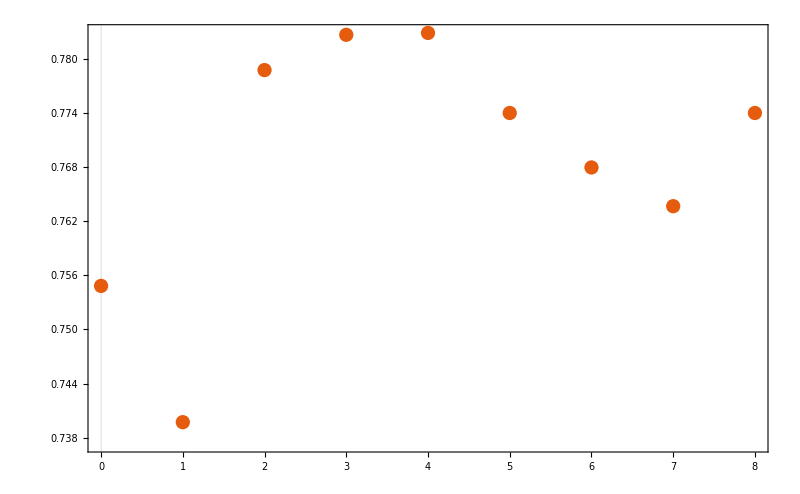

```mathematica
densPlot=ListPlot[densPoints,PlotTheme->"Scientific",ImageSize->800, ImagePadding->120]
```

```mathematica
SetDirectory["/home/carla/GDC/DENS/"]
Put[dens, "GDC_DENS.txt"]
Export["GDC_DENS.jpeg",densPlot]
```

/home/carla/GDC/DENS

GDC_DENS.jpeg

```mathematica
dlb=nEFUN["DLB",pos,"NUM"]
prozEFunc["DLB", dlb,sens]
dlbB=Map[dlb[[#]]&,{1,3,5,7,9,11,13,15,17}]
numCONE
dlbBCORE=dlbB-numCONE
Map[dlbBCORE[[#]]+numCONE[[#+1]]&,Range[Length[numCONE]-1]]
dlbA=Map[dlb[[#]]&,{2,4,6,8,10,12,14,16}]
```

{15,16,22,28,22,24,25,29,33,34,36,36,39,40,42,45,43}

sentPT {46,65,65,84,84,88,88,102,102,110,110,117,117,123,123,132,132}

{0.326,0.246,0.338,0.333,0.262,0.273,0.284,0.284,0.324,0.309,0.327,0.308,0.333,0.325,0.341,0.341,0.326}

{15,22,22,25,33,36,39,42,43}

{8,9,15,17,21,22,22,23,26}

{7,13,7,8,12,14,17,19,17}

{16,28,24,29,34,36,40,45}

{16,28,24,29,34,36,40,45}

```mathematica
eSIZE=Association[Map[names[[#]]->nEFUN[names[[#]],pos,"NUM"]&,Range[Length[names]]]]
ePROZ=Association[Map[names[[#]]->prozEFunc[names[[#]],Values[eSIZE][[#]],sens]&,Range[Length[names]]]]
```

<|DLB→{15,16,22,28,22,24,25,29,33,34,36,36,39,40,42,45,43},MUR→{20,26,25,27,30,34,37,38,41,41,43,44,42,45,45},LYE→{19,25,22,24,26,30,31,32,35,35,36,37,41,44,43},PHI→{20,22,24,28,32,33,35,35,36,37,40,43,41},SED→{25,29,34,35,38,38,39,40,44,47,44},AUS→{40,41,44,47,43}|>

<|DLB→{0.484,0.32,0.44,0.406,0.319,0.329,0.342,0.333,0.379,0.358,0.379,0.353,0.382,0.37,0.389,0.385,0.368},MUR→{0.4,0.377,0.362,0.37,0.411,0.391,0.425,0.4,0.432,0.402,0.422,0.407,0.389,0.385,0.385},LYE→{0.38,0.362,0.319,0.329,0.356,0.345,0.356,0.337,0.368,0.343,0.353,0.343,0.38,0.376,0.368},PHI→{0.29,0.301,0.329,0.322,0.368,0.347,0.368,0.343,0.353,0.343,0.37,0.368,0.35},SED→{0.342,0.333,0.391,0.368,0.4,0.373,0.382,0.37,0.407,0.402,0.376},AUS→{0.392,0.38,0.407,0.402,0.368}|>

```mathematica
N[{2./20,5./20,8./20}]
{8./19,4./19}
```

{0.1,0.25,0.4}

{0.421053,0.210526}

```mathematica
devABFIN=Get["/home/carla/GDC/Comparisons/New_REKO_19_02_21/Veritism/E_DEDAB/gdc_DEDAB_E_DEV.txt"][[-1]];
```

```mathematica
(*eFALSE=Association[Map[names[[#]]->eFUN[persInds[[#]], Drop[pos,persDrops[[#]]],devABFIN,"FAL"]&,Range[Length[names]]]];*)
(*eFUN[name_, pos_,dev_, mod_]*)
eFALSENUM=Association[Map[names[[#]]->eFUN[names[[#]], pos,devABFIN,"FALN"]&,Range[Length[names]]]]
eTRUENUM=Association[Map[names[[#]]->eFUN[names[[#]], pos,devABFIN,"TRUN"]&,Range[Length[names]]]]
eFALSEPROZ=Association[Map[names[[#]]->prozEFunc[names[[#]],Values[eFALSENUM][[#]],sens]&,Range[Length[names]]]]
eTRUEPROZ=Association[Map[names[[#]]->prozEFunc[names[[#]],Values[eTRUENUM][[#]],sens]&,Range[Length[names]]]]
```

<|DLB→{5,5,5,5,1,1,0,0,1,1,2,2,3,3,5,5,0},MUR→{2,2,2,2,2,2,4,4,4,4,7,7,1,1,0},LYE→{2,2,2,2,2,2,3,3,5,5,5,5,3,3,0},PHI→{0,0,0,0,0,0,1,1,2,2,3,3,0},SED→{0,0,3,3,4,4,5,5,6,6,0},AUS→{1,1,2,2,0}|>

<|DLB→{9,10,14,20,18,20,22,26,28,29,30,30,32,33,33,36,39},MUR→{15,21,18,20,22,26,25,26,29,29,28,29,35,38,38},LYE→{14,20,16,18,20,24,24,25,26,26,27,28,34,37,37},PHI→{17,19,21,25,28,29,30,30,30,31,33,36,37},SED→{21,25,26,27,29,29,29,30,33,36,39},AUS→{35,36,38,41,39}|>

<|DLB→{0.161,0.1,0.1,0.072,0.014,0.014,0.,0.,0.011,0.011,0.021,0.02,0.029,0.028,0.046,0.043,0.},MUR→{0.04,0.029,0.029,0.027,0.027,0.023,0.046,0.042,0.042,0.039,0.069,0.065,0.009,0.009,0.},LYE→{0.04,0.029,0.029,0.027,0.027,0.023,0.034,0.032,0.053,0.049,0.049,0.046,0.028,0.026,0.},PHI→{0.,0.,0.,0.,0.,0.,0.011,0.01,0.02,0.019,0.028,0.026,0.},SED→{0.,0.,0.034,0.032,0.042,0.039,0.049,0.046,0.056,0.051,0.},AUS→{0.01,0.009,0.019,0.017,0.}|>

<|DLB→{0.29,0.2,0.28,0.29,0.261,0.274,0.301,0.299,0.322,0.305,0.316,0.294,0.314,0.306,0.306,0.308,0.333},MUR→{0.3,0.304,0.261,0.274,0.301,0.299,0.287,0.274,0.305,0.284,0.275,0.269,0.324,0.325,0.325},LYE→{0.28,0.29,0.232,0.247,0.274,0.276,0.276,0.263,0.274,0.255,0.265,0.259,0.315,0.316,0.316},PHI→{0.246,0.26,0.288,0.287,0.322,0.305,0.316,0.294,0.294,0.287,0.306,0.308,0.316},SED→{0.288,0.287,0.299,0.284,0.305,0.284,0.284,0.278,0.306,0.308,0.333},AUS→{0.343,0.333,0.352,0.35,0.333}|>

```mathematica
pointsE2=Association[Map[Function[y,
y->Map[Function[x,{eFALSENUM[y][[x]],eTRUENUM[y][[x]],h[y, Length[timesteps]][[x]]}],Range[Length[ePROZ[y]]]]],names]]
range={{Min[Flatten[Values[pointsE2],1][[All,1]]],Max[Flatten[Values[pointsE2],1][[All,1]]]},
{Min[Flatten[Values[pointsE2],1][[All,2]]],Max[Flatten[Values[pointsE2],1][[All,2]]]}}
```

<|DLB→{{5,9,1},{5,10,2},{5,14,3},{5,20,4},{1,18,5},{1,20,6},{0,22,7},{0,26,8},{1,28,9},{1,29,10},{2,30,11},{2,30,12},{3,32,13},{3,33,14},{5,33,15},{5,36,16},{0,39,17}},MUR→{{2,15,3},{2,21,4},{2,18,5},{2,20,6},{2,22,7},{2,26,8},{4,25,9},{4,26,10},{4,29,11},{4,29,12},{7,28,13},{7,29,14},{1,35,15},{1,38,16},{0,38,17}},LYE→{{2,14,3},{2,20,4},{2,16,5},{2,18,6},{2,20,7},{2,24,8},{3,24,9},{3,25,10},{5,26,11},{5,26,12},{5,27,13},{5,28,14},{3,34,15},{3,37,16},{0,37,17}},PHI→{{0,17,5},{0,19,6},{0,21,7},{0,25,8},{0,28,9},{0,29,10},{1,30,11},{1,30,12},{2,30,13},{2,31,14},{3,33,15},{3,36,16},{0,37,17}},SED→{{0,21,7},{0,25,8},{3,26,9},{3,27,10},{4,29,11},{4,29,12},{5,29,13},{5,30,14},{6,33,15},{6,36,16},{0,39,17}},AUS→{{1,35,13},{1,36,14},{2,38,15},{2,41,16},{0,39,17}}|>

{{0,7},{9,41}}

```mathematica
threDOJ["MUR"]
Range[Length[threDOJ["MUR"]]]
```

{{10,11/18},{11,34/67},{12,34/67},{15,1},{16,1},{17,1}}

{1,2,3,4,5,6}

```mathematica
pDOJass=Association[Map[pointsFunc[#,threDOJ, pointsE2]&,names]]
pZass=Association[Map[pointsFunc[#,threZ, pointsE2]&,names]];
pFass=Association[Map[pointsFunc[#,threF, pointsE2]&,names]];
```

<|DLB→{{0,39,1}},MUR→{{4,26,11/18},{4,29,34/67},{4,29,34/67},{1,35,1},{1,38,1},{0,38,1}},LYE→{{5,27,2/3},{5,28,2/3},{3,34,1},{0,37,1}},PHI→{{0,28,7/10},{0,29,11/15},{1,30,7/10},{1,30,7/10},{2,30,7/10},{2,31,7/10},{3,33,1},{3,36,1},{0,37,1}},SED→{{0,39,1}},AUS→{{1,35,11/15},{1,36,11/15},{2,38,1},{2,41,1},{0,39,1}}|>

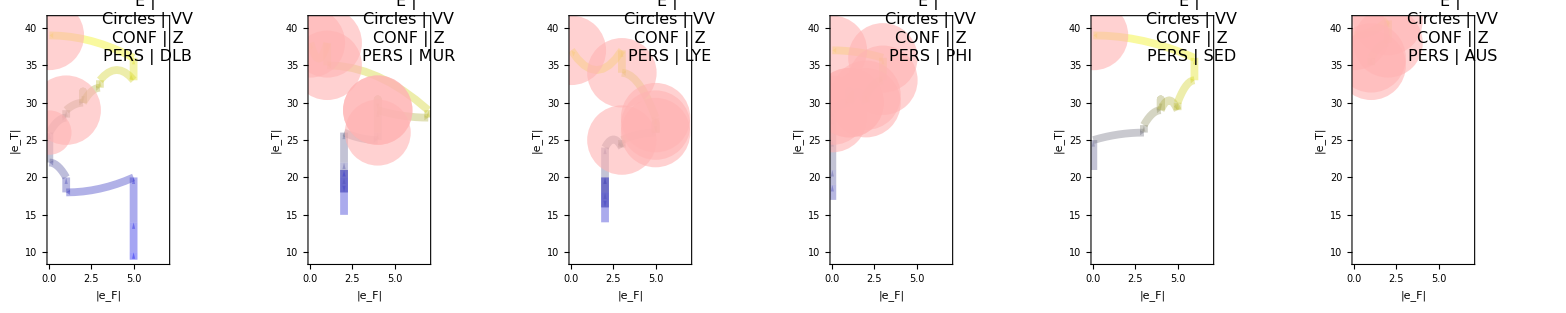

```mathematica
dojTHRE=Map[singlePlot2[#, pointsE2[#],pDOJass[#],col2, "DOJ",range,0.095,0.095]&,names];
dojGrid=Grid[{dojTHRE[[1;;6]]}];
zTHRE=Map[singlePlot2[#, pointsE2[#],pZass[#],col2, "Z",range,0.095,0.095]&,names];
zGrid=Grid[{zTHRE[[1;;6]]}]
fTHRE=Map[singlePlot2[#, pointsE2[#],pFass[#],col2, "F",range,0.095,0.095]&,names];
fGrid=Grid[{fTHRE[[1;;6]]}];
```

```mathematica
Export["DOJ_E.jpeg", dojGrid]
Export["Z_E.jpeg", zGrid]
Export["F_E.jpeg", fGrid]
```

DOJ_E.jpeg

Z_E.jpeg

F_E.jpeg